```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/summary

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

#### 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.085874

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}/.m2->1//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √(-((-4+x4) x4)) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
int1=Integrate[(baik 2Pi^2/.m2->1)/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
(*Total[toint2]*)
int2=Integrate[Simplify[toint2],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2,logs][[1]];
(*Total[toint3]*)
int3=Integrate[toint3,x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=Coefficient[int3,logs][[1]]
(*Quartic polynomial*)
toint4//FullSimplify//PowerExpand// FullSimplify
```

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
EllipticSunrise = 1/(√(4-x4) √x4 √(pp^2+(1-x4)^2-2 pp (1+x4)));
```

```mathematica
(*per=Import["../phi3/2loop/PERIODS/omega0.m"];*)
(*periods={ω0[ρ]->per[[1]] /.F2[g[ρ,a_]] -> ρ^a,ω1[ρ]->per[[2]] /.F2[g[ρ,a_]] -> ρ^a /.F2[g[log,1],g[ρ,m_]]-> L ρ^m};*)
```

```mathematica
periods=Import["./periods/elliptic_sunrise_2l/periods.m"];
```

```mathematica
Collect[Series[Sqrt[3] EllipticSunrise/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x4,1,-1}], {x4,1}]//Expand
periods[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

#### 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.040641

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=(baik 2 π^3/. m2-> 1)/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2, x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = Coefficient[int2,logs];
int3=Integrate[toint3, x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = Coefficient[int3,logs][[1]];
int4=Integrate[toint4, x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = Coefficient[int4,logs][[1]]
```

1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

```mathematica
K3Banana=1/(√(4-x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
periodBanana=Import["./periods/k3_banana_3l/periods.m"];
```

```mathematica
(*
check that the period is corect
*)
```

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

#### Triangle sunrise

```mathematica
K3Banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

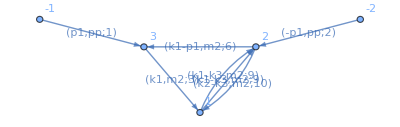

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.043718

```mathematica
toint=baik/(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify
```

-ⅈ/(π^3 x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-((-4+x6) x6)) √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=K3Banana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/(π^3 (-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]
```

-1/(4 π^3 √(-4+pp) √pp)

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periods.m"][[1]];
```

```mathematica
toexpand =integrand Pi^3 (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandroots/expandroots.m",tocheck];*)
expandRoot= Import["./expandroots/expandroots.m"];
```

```mathematica
Print["done"]
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
periodBanana=Expand[periodBanana F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] periodBanana+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[periodBanana /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)

#### 4 loop banana (don’t have the period yet)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik =Pi^4  baik // FullSimplify;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.102873

```mathematica
maxcutIntegrand=baik /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} // FullSimplify // PowerExpand//FullSimplify
```

ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

```mathematica
series=Collect[Collect[Series[1/√(-pp^2-(-1+x8)^2+2 pp (1+x8)), {pp,0,20}]//Normal, {pp}, Simplify], {pp}, PowerExpand];
```

```mathematica
Series[(series /. pp^a_ /; a> 5->0) /√(-x7^2-(-1+x8)^2+2 x7 (1+x8)), {x8,1,-1}]//Normal;
residue=Residue[%,{x8,1}];
residue=Collect[Collect[residue, {pp},PowerExpand], {pp}, Simplify];
```

#### 4 loop triangle bubble - sunrise easy (elliptic)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

{-Graphics-,-Graphics-}

"Total runtime= "  0.048498

-1/(√(-(x1-x3)^2+2 (2+x1+x3) x7-x7^2) √(-(x2-x6)^2+2 (2+x2+x6) x7-x7^2) √(-(x4-x6)^2+2 (2+x4+x6) x8-x8^2) √(-pp^2-(1+x5-x8)^2+2 pp (1+x5+x8)))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
int1=Integrate[toint, x7];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
```

-ⅈ/((-4+x7) x7 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

-ⅈ/(4 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

#### 4 loop triangle bubble - sunrise hard

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, (k3+k4)^2-m2, (k4 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] +2sp[k3,k4] + sp[k4,k4]-m2,
sp[k4,k4] + pp + k1k1 + 2 k1p1 +2 sp[k4,P1]-m2, sp[k4,P1], sp[k3,P1]}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2,x3, x40,x41}]],sps]//Flatten;
```

{-m2+sp[k3,k3],-m2+sp[k3,k3]+2 sp[k3,k4]+sp[k4,k4],k1k1+2 k1p1-m2+pp+sp[k4,k4]+2 sp[k4,P1],sp[k4,P1],sp[k3,P1]}

```mathematica
external = {P1};
allmomenta = {P1,k3,k4};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-2-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
firstLoopBaik
```

(k1k1+2 k1p1+pp)^((2-d)/2) (-((k1k1+2 k1p1+pp) (m2+x1) (k1k1+2 k1p1-m2+pp-x3+2 x40))-1/2 (k1k1+2 k1p1+pp) (k1k1+2 k1p1-m2+pp-x1+x2-x3+2 x40) sp[k4,k3]+1/2 x40 (k1k1+2 k1p1-m2+pp-x1+x2-x3+2 x40) sp[P1,k3]+(k1k1+2 k1p1-m2+pp-x3+2 x40) x41 sp[P1,k3]-(m2+x1) x40 sp[P1,k4]+x41 sp[k4,k3] sp[P1,k4])^(1/2 (-4+d))

```mathematica
(*firstLoopBaik /. d-> 2 /. {x1->0, x2->0,x3->0} // FullSimplify
Integrate[%,x41]//TrigToExp;
(Coefficient[%,Log[1-(ⅈ √(-k1k1-2 k1p1+m2-pp-2 x40) (x40+2 x41))/(√(k1k1^3+8 k1p1^3-3 m2^2 pp+2 m2 pp^2+pp^3+4 m2 pp x40+4 pp^2 x40+3 m2 x40^2+5 pp x40^2+2 x40^3+4 k1p1^2 (2 m2+3 pp+4 x40)+k1k1^2 (6 k1p1+2 m2+3 pp+4 x40)+2 k1p1 (-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40))+k1k1 (12 k1p1^2-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40)+4 k1p1 (2 m2+3 pp+4 x40))))]] //FullSimplify)/.pp->-k1k1-2 k1p1+ PP*)
```

```mathematica
firstLoopBaik/.d-> 10//Variables
```

{k1k1,k1p1,pp,m2,x1,x40,x3,x2,x41}

```mathematica
(* Third loop, I have k1, k1+k2,  k1.p1 --> triangle kinematics *)
(*  
(k1)^2-m2, (k1+k2)^2-m2, (k1 + p1)^2-m2
*)
```

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x4,x5,x42}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x4,sp[k1,k2]→-k2k2/2-x4/2+x5/2,sp[k1,p1]→-m2/2-pp/2-x4/2+x42/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
```

```mathematica
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x4,x42,x5}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
```

```mathematica
propsecondloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propsecondloop , {x6,x43}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x6,sp[k2,p1]→x43}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
```

```mathematica
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10};
Variables[baik/. d-> 2]
```

{m2,x1,x7,x8,pp,x3,x4,x9,x2,x10,x5,x6}

```mathematica
baikd2=baik /. d-> 2//FullSimplify
```

16/((4 (m2+x1) x7^2+4 (m2+x1-x2+x3-2 x7) x7 x8+4 (m2+x3-2 x7) x8^2-(3 m2^2-x1^2+2 x1 (x2+x3-2 x7)+2 m2 (x1+x2+x3-2 x7)-(x2-x3+2 x7)^2+4 x7 x8+4 x8^2) x9+2 (m2+x1+x2-x3+2 x7) x9^2+x9^3) (m2^3+pp^2 x6+x4 (4 x10^2+x4 x6-2 x10 (x4-x5+x6))+m2^2 (-pp-2 x10+2 x4+x6-2 x9)+2 (-x4 x6+x10 (x4-x5+x6)) x9+x6 x9^2+pp (x4^2-2 x4 x5+(x5-x6)^2-2 x10 (x4-x5+x6)-2 x6 x9)+m2 (pp^2+4 x10^2+(x4-x9) (x4+2 x6-x9)-2 pp (x10+x5+x9)+2 x10 (-2 x4+x5-x6+x9))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0,x6->0}//FullSimplify;
```

```mathematica
int1=Collect[Integrate[maxcut ,x7]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]//FullSimplify
int2 = Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]]//FullSimplify//FullSimplify
```

(4 ⅈ)/(m2 √(m2-2 x8+x9) √(-((3 m2+2 x8-x9) (-x8^2+m2 x9))) (m2^2+pp^2+4 x10^2+2 x10 x9+x9^2-2 pp (x10+x9)-m2 (pp+2 (x10+x9))))

-2/(√3 m2 √(m2-2 x8+x9) √(-((3 m2+2 x8-x9) (-x8^2+m2 x9))) √(m2^2+(pp-x9)^2-2 m2 (pp+x9)))

(2 ⅈ)/(√3 √(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(-x9+1/4 (-3+x8+x9)^2))

```mathematica
K3banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6))) /. {x6 -> x9, x5 -> x8} //Expand // FullSimplify
((toint3 Sqrt[3] /2(-I)/. m2->1 //Expand // FullSimplify) /. x8 -> x8/2  /.x8 -> x8 -3 + x9//FullSimplify // PowerExpand//FullSimplify//PowerExpand ) /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]/.x8 -> x8 +4 /. x8 -> -x8//FullSimplify//PowerExpand
```

1/(√(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

-(2 ⅈ)/(√(4-x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

### Integral families

```mathematica
(* easy triangle bubble sunrise *)
(*
integralfamilies:-name:topoA
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1+p1",m2]
-["k1+k2",m2]
-["k2",m2]
-["k2+k3",m2]
-["k4",m2]
-["k3+k4",m2]
-{bilinear:[["k1","k2"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
# cut_propagators:[1,2,3,4,5,6]
*)

(* difficult triangle sunrise bubble  *)
(* 
integralfamilies:-name:topoB
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1",m2]
-["k1+p1+k3",m2]
-["k3+k4",m2]
-["k4",m2]
-["k1+k2",m2]
-["k2",m2]
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k2","k3"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
cut_propagators:[1,2,3,4,5,6]
*)
```